# Costa’s Minimal Surface with Minimal Fuss

## Andrej Bauer

Dedicated to all students who have never gone the extra mile.

## Costa’s surface

Costa’s minimal surface is a surface with some amazing mathematical properties which we are not going to discuss here. We are only concerned with how to draw it. Recall that a surface S ⊂ ℝ^3 can be represented by a map f: Ω → ℝ^3 where Ω ⊂ ℝ^2. For each point (x,y) ∈ Ω we get a point f(x,y) ∈ ℝ^3. As (x,y) ranges over Ω, the values f(x,y) range over S.

Costa’s surface is parametrized by the function costa defined below. The region Ω is the square [0,1]×[0,1].

```mathematica
ClearAll[g,e,costa]
g=WeierstrassInvariants[{1/2,I/2}];
e = WeierstrassP[1/2,g];

costa::usage="Compute a point on the Costa's minimal surface.";

costa[x_,y_]:=
With[
{
wz1=WeierstrassZeta[x+I y,g],
wz23=WeierstrassZeta[x+I y-1/2,g]-WeierstrassZeta[x+I y-I/2,g],
wp=WeierstrassP[x+I y,g]
},
{
(Pi x+Pi^2/(4Re[e])-Re[wz1]+Pi/(2Re[e])*Re[wz23])/2,
(Pi y+Pi^2/(4Re[e])+Im[wz1]+Pi/(2Re[e])*Im[wz23])/2,
(Sqrt[2Pi]/4)*(Log[Abs[wp-e]]-Log[Abs[wp+e]])
}
]
```

This already suffices for a nice picture of the surface:

```mathematica
ParametricPlot3D[costa[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

It is instructive to plot the magnitude of costa[x,y]:

```mathematica
Plot3D[Norm[costa[x,y]],{x,0,1},{y,0,1}]
```

-Graphics3D-

As you can see, there are poles at the corners of the unit square, as well as the midpoints of the sides. Because of these, the surface streches out to infinity. We should be careful about how we draw things near the poles.

## Computing the normals to the surface

If you want to draw Costa’s surface with a raytracer such as PovRay, you may wish to compute the normals to the surface. So let us do that as well. Recall that the normal at f[x_0,y_0] to a surface parametrized by a map f is the vector product f_x[x_0,y_0] × f_y[x_0,y_0] where f_x and f_y are the partial derivatives of f. The partial derivatives of costa are beyond Mathematica’s abilities, so we need to tell it how to compute them.

The first two components of costa[x,y] are real parts of holomorphic functions. For these, the partial derivative and the real part Re commute. The third component must be computed by hand because it is not holomorphic. It gets tricky to get the derivatives right (at least for me), so we’re going to double-check them by numerical integration.

```mathematica
ClearAll[checkDerivative]
checkDerivative::usage="Check that g is the derivative of f by integarting from x0 to x1.";
checkDerivative[f_,g_,{x_,x0_,x1_}]:=
N[(f/.x->x1)-(f/.x->x0)]-NIntegrate[N[g], {x, x0, x1}]
```

We need the partial derivatives of (x,y)↦log|f(x+𝕚 y)| where f is holomorphic. This requires a bit of work. First we have the partial derivatives of (x+𝕚y)↦log|x+𝕚 y|:

```mathematica
ClearAll[logAbsDX,logAbsDY]
logAbsDX[z_]:=Re[z]/(Re[z]^2+Im[z]^2)
logAbsDY[z_]:=Im[z]/(Re[z]^2+Im[z]^2)
```

Then there will be the chain rule which allows us to compute the derivatives of (x,y)↦log|f(x+𝕚 y)|, given f and its derivative f'

```mathematica
ClearAll[logAbsChainX, logAbsChainY]
logAbsChainX[f_,fPrime_]:=logAbsDX[f]*Re[fPrime]+logAbsDY[f]*Im[fPrime]
logAbsChainY[f_,fPrime_]:=-logAbsDX[f]*Im[fPrime]+logAbsDY[f]*Re[fPrime]
```

The partial derivative of costa with respect to x:

```mathematica
ClearAll[costaX]
costaX[x_,y_]:=
With[
{
wz1D=-WeierstrassP[x+I*y,g],
wz23D=WeierstrassP[x+I*y-I/2,g]-WeierstrassP[x+I*y-1/2,g],
wp=WeierstrassP[x+I*y,g],
wpD=WeierstrassPPrime[x+I*y,g]
},
{
(Pi -Re[wz1D]+Pi/(2Re[e])*Re[wz23D])/2,
(Im[wz1D]+Pi/(2Re[e])*Im[wz23D])/2,
(Sqrt[2Pi]/4)*(logAbsChainX[wp-e,wpD]-logAbsChainX[wp+e,wpD])
}
]
```

Did we get it right? If so, we should get a triple of zeroes:

```mathematica
checkDerivative[costa[x,0.2],costaX[x,0.2],{x,0.2,0.7}]
```

{3.24585×10^-12,7.77156×10^-16,7.21645×10^-16}

Good enough.

The partial derivative of costa with respect to y:

```mathematica
ClearAll[costaY]
costaY[x_,y_]:=
With[
{
wz1D=-WeierstrassP[x+I*y,g],
wz23D=WeierstrassP[x+I*y-I/2,g]-WeierstrassP[x+I*y-1/2,g],
wp=WeierstrassP[x+I*y,g],
wpD=WeierstrassPPrime[x+I*y,g]
},
{
(Im[wz1D]-Pi/(2Re[e])*Im[wz23D])/2,
(Pi +Re[wz1D]+Pi/(2Re[e])*Re[wz23D])/2,
(Sqrt[2Pi]/4)*(logAbsChainY[wp-e,wpD]-logAbsChainY[wp+e,wpD])
}
]
```

And did we get this derivative right?

```mathematica
checkDerivative[costa[0.2,y],costaY[0.2,y],{y,0.2,0.7}]
```

{-1.11022×10^-16,3.24585×10^-12,-4.996×10^-16}

Excellent, now we can compute normals to the surface:

```mathematica
ClearAll[costaNormal]
costaNormal::usage="Compute the normal to Costa's surface at a given point.";
costaNormal[x_,y_]:=Normalize[N[Cross[costaX[x,y],costaY[x,y]]]]
```

Here is a simple function that draws little arrows for normals.

```mathematica
ClearAll[normalArrow]
normalArrow[x_,y_]:=
With[{a=N[costa[x,y]], b =costaNormal[x,y]},
Arrow[{a,a+b}]]
```

## Triangulation of the surface

We want to compute a triangulation of the surface. This can be useful for drawing Costa’s surface with a program such as PovRay. The trouble is that we must avoid the singularities at the corners and the midpoints of the sides of [0,1]×[0,1].

### Generating the mesh

First we generate a mesh of the area which we will use for the parametrization of the surface. We excise from [0,1]×[0,1] small circles with radius r_1 at the corners and small circles with radius r_2 at midpoints of sides. We call these holes.

```mathematica
ClearAll[outsideCircle,outsideHoles]
outsideCircle::usage="Is p outside the circle centered at c with radius r?";
outsideCircle[c_,r_][p_]:=(p-c).(p-c)>r^2

outsideHoles::usage"Is p outside the holes?";
outsideHoles[r1_,r2_][p:{_,_}]:=
And @@ Flatten[Table[outsideCircle[{u,v},r1][p],{u,0,1},{v,0,1}],1]&&
outsideCircle[{0.5,0},r2][p] &&
outsideCircle[{0.5,1},r2][p] &&
outsideCircle[{0,0.5},r2][p] &&
outsideCircle[{1,0.5},r2][p]
```

Next we write functions that triangulate the unit square without the points.

```mathematica
ClearAll[rectGrid,arcPoints,edgePoints,costaGrid]

rectGrid[r1_,r2_,n_]:=Select[Flatten[Table[N[{i/n,j/n}],{i,1,n-1},{j,1,n-1}],1],outsideHoles[r1,r2]]

arcPoints[x_,y_,r_,alpha_,beta_,n_]:=
Table[
{x+r*Cos[(alpha*(n-i)+beta*i)/n],
y+r*Sin[(alpha*(n-i)+beta*i)/n]},
{i,0,n}]

edgePoints[r1_,r2_,n_,m_,l_]:=
With[{seg=Join[
Table[(r1*(n-i)+(0.5-r2)*i)/n,{i,1,n-1}],
Table[((0.5+r2)*(n-i)+(1-r1)*i)/n,{i,1,n-1}]]},
Join[
Flatten[Outer[List,seg,{0}],1],
Flatten[Outer[List,seg,{1}],1],
Flatten[Outer[List,{0},seg],1],
Flatten[Outer[List,{1},seg],1],
arcPoints[0,0,r1,0,Pi/2,m],
arcPoints[1,0,r1,Pi/2,Pi,m],
arcPoints[1,1,r1,Pi,3Pi/2,m],
arcPoints[0,1,r1,3Pi/2,2Pi,m],
arcPoints[0.5,0,r2,0,Pi,l],
arcPoints[0.5,1,r2,Pi,2Pi,l],
arcPoints[0,0.5,r2,3Pi/2,5Pi/2,l],
arcPoints[1,0.5,r2,Pi/2,3Pi/2,l]
]
]

costaGrid::usage = "costaGrid[r1,r2,k,n,m,l] generates a point grid suitable for triangulation, where r1 and r2 are the radii of the holes, and k, n, m, l determine the density of the grid inside the area, on the straight edges, on the corner holes and the side holes, respectively.";
costaGrid[r1_,r2_,k_,n_,m_,l_]:=
N@Join[rectGrid[1.1*r1,1.1*r2,k],edgePoints[r1,r2,n,m,l]]
```

A picture of the grid will explain what we are going for:

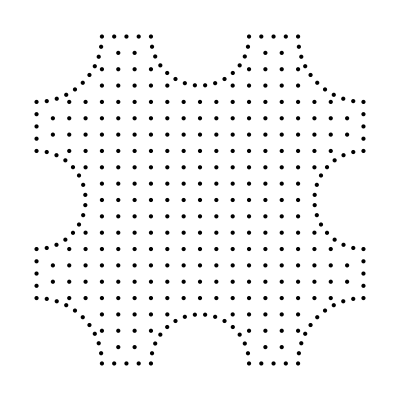

```mathematica
Graphics[Point/@costaGrid[0.2,0.15,20,4,10,15]]
```

We need to triangulate the mesh. The Mathematica function ListDensityPlot computed the Delaunay triangulation in a much more useful way than DelaunayTriangulation, so this is what we use:

```mathematica
ClearAll[triangles]
triangles::usage="Triangulate the given set of points.";
triangles[points_]:=
First@Cases[
ListDensityPlot[ArrayPad[points,{{0,0},{0,1}}]],
Polygon[a_]:>a,
Infinity]
```

```mathematica
ClearAll[barycenter]
barycenter::usage="Compute the barycenter of the triangle whose vertices are given by i,j,k.";
barycenter[pts_,{i_,j_,k_}]:=(pts⟦i⟧+pts⟦j⟧+pts⟦k⟧)/3
```

The function triangles triangulates the convex hull of the given points. To get the desired triangulation, we filter out those triangles whose barycenters are inside the holes:

```mathematica
ClearAll[costaTriangulate]
costaTriangulate::usage="Return the points and the triangles of a mesh for drawing Costa's surface.";
costaTriangulate[r1_,r2_,k_,m_,n_,l_]:=
With[{pts=costaGrid[r1,r2,k,m,n,l]},
{pts,
Select[triangles[pts],outsideHoles[r1,r2][barycenter[pts,#]]&]
}
]
```

A picture of the triangulation (the holes are made bigger than necessary):

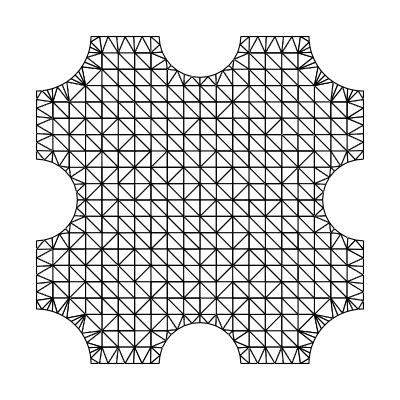

```mathematica
ClearAll[grid,trs]
{grid,trs}=costaTriangulate[1/6,1/8,20,8,16,16];
Graphics[{EdgeForm[Black],FaceForm[White],GraphicsComplex[N[grid],Polygon/@trs]}]
```

We can also draw the surface with small triangles, together with the normals at the vertices:

```mathematica
ClearAll[grid,trs,costaA,costaT]
{grid,trs}=costaTriangulate[1/10,1/30,10,5,10,10];
costaA=Graphics3D[normalArrow@@@grid];
costaT=Graphics3D[{EdgeForm[Black],FaceForm[White],GraphicsComplex[N[costa @@@grid],Polygon/@trs]}];
Show[costaA,costaT]
```

-Graphics3D-

### Saving the data

A utility function for saving the data into a CSV file, suitable for further processing.

```mathematica
ClearAll[costaCSV]
costaCSV::usage="Save Costa's surface data to the given CSV file";
costaCSV[file_,r1_,r2_,k_,m_,n_,l_]:=
Module[{grid,trs,data},
{grid,trs}=costaTriangulate[r1,r2,k,m,n,l];
data=Join[
N[{{r1,r2,k,m,n,l}}],
{Length[grid]},
N[costa@@@grid],
{Length[grid]},
N[costaNormal@@@grid],
{Length[trs]},
trs-1
];
Export[file,data]
]
```

```mathematica
costaCSV["costa.csv",1/10,1/30,40,20,40,40]
```

costa.csv